# Dynamic Analysis

-Graphics-

In the dynamic analysis, the scope is to derive the equation of motion of the manipulator. 
-Graphics---> Lagrangian equation of motion 
In this example, we study a very simple configuration just composed of a link rotating around the x axis.

## 1. Direct Kinematics

The Lagrangian component L is made of the kinematic and the potential energy. 
In order to get the kinematic term, we need to compute the velocity of the masses.

```mathematica
Mrotxtrasl[α_,point_]:={{1,0,0,point⟦1⟧},{0,Cos[α],-Sin[α],point⟦2⟧},{0,Sin[α],Cos[α],point⟦3⟧},{0,0,0,1}} (*Roto-trasl.matrix about x axis*)
```

```mathematica
Mrotxtrasl[α,{p1,p2,p3}]//MatrixForm
```

(1 | 0 | 0 | p1
0 | Cos[α] | -Sin[α] | p2
0 | Sin[α] | Cos[α] | p3
0 | 0 | 0 | 1)

```mathematica
EE={0,L *Cos[θ[t]],L Sin[θ[t]],1}; (*Point E w.r.t.RF0*)
```

```mathematica
M01=Mrotxtrasl[θ[t],EE];
M01//MatrixForm (*Transformation matrix from RF0-RF1*)
```

(1 | 0 | 0 | 0
0 | Cos[θ[t]] | -Sin[θ[t]] | L Cos[θ[t]]
0 | Sin[θ[t]] | Cos[θ[t]] | L Sin[θ[t]]
0 | 0 | 0 | 1)

Now that we know the transformation matrix of 01, we can compute the velocity matrix.

```mathematica
W01=Simplify[D[M01,t].Inverse[M01]];(*Velocity Matrix*)
W01//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | -θ'[t] | 0
0 | θ'[t] | 0 | 0
0 | 0 | 0 | 0)

The same velocity matrix can be obtained by making use of the elicoidal transformation matrix.

```mathematica
Lrotx={{0,0,0,0},{0,0,-1,0},{0,1,0,0},{0,0,0,0}};Lrotx//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | -1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
L01=Lrotx;
L01*D[θ[t],t]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | -θ'[t] | 0
0 | θ'[t] | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W01.EE//MatrixForm(*Velocity of point EE in theRF0*)
```

(0
-L Sin[θ[t]] θ'[t]
L Cos[θ[t]] θ'[t]
0)

## 2. Lagrangian Components

We are going to calculate now the Lagrangian components T (kinematic energy term) and U (potential energy term). 
Let’s start with the kinematic energy one. 
Having 2 masses, we’ll need to calculate to 2 different kinematic contributions. For both of them we need the pseudo inertia tensor.
Mass 1 correspond to the mass of the arm and mass 2 correspond to the mass of the load.

-Graphics-

-Graphics-

The tensor matrix is referred to a specific reference frame. 
So we start by expresses the tensor matrix of a specific mass in its local reference frame and, once we have it, we express it in the absolute reference frame.

```mathematica
J11={{0,0,0,0},{0,1/3*m1*L^2,0,-m1*L/2},{0,0,0,0},{0,-m1*L/2,0,m1}};(*Pseudo Inertia Tensor of mass1 wrt ref 1. The mass is considered to be distributed along the link*)
J11//MatrixForm
```

(0 | 0 | 0 | 0
0 | (L^2 m1)/3 | 0 | -(L m1)/2
0 | 0 | 0 | 0
0 | -(L m1)/2 | 0 | m1)

To express the tensor matrix in the absolute reference frame I need to compute the following transformation:

-Graphics-

```mathematica
J10=M01.J11.Transpose[M01];
J10//MatrixForm
```

(0 | 0 | 0 | 0
0 | 1/3 L^2 m1 Cos[θ[t]]^2 | 1/3 L^2 m1 Cos[θ[t]] Sin[θ[t]] | 1/2 L m1 Cos[θ[t]]
0 | 1/3 L^2 m1 Cos[θ[t]] Sin[θ[t]] | 1/3 L^2 m1 Sin[θ[t]]^2 | 1/2 L m1 Sin[θ[t]]
0 | 1/2 L m1 Cos[θ[t]] | 1/2 L m1 Sin[θ[t]] | m1)

Now, I have all the elements to compute the kinetic energy T of mass1.

-Graphics-

```mathematica
T1=Simplify[Tr[(1/2)*W01.J10.Transpose[W01]]](*Kinetic energy of robotarm.Tr command computes the trace of the input matrix*)
```

1/6 L^2 m1 θ'[t]^2

Let’s do the same analysis for mass 2. We start with the pseudo inertia matrix.

```mathematica
J21={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,m2}}; (*Pseudo Inertia Tensor of mass 2 wrt ref1*)
J21//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | m2)

Notice that we don’t have any inertial term, just translational. This is because the mass is in the origin of the reference frame with respect to we are expressing it onto.

```mathematica
J20=M01.J21.Transpose[M01]; (*Pseudo Inertia Tensor of mass 2 wrt absolute reference frame *)
J20//MatrixForm
```

(0 | 0 | 0 | 0
0 | L^2 m2 Cos[θ[t]]^2 | L^2 m2 Cos[θ[t]] Sin[θ[t]] | L m2 Cos[θ[t]]
0 | L^2 m2 Cos[θ[t]] Sin[θ[t]] | L^2 m2 Sin[θ[t]]^2 | L m2 Sin[θ[t]]
0 | L m2 Cos[θ[t]] | L m2 Sin[θ[t]] | m2)

```mathematica
W02 = W01; (*velocity matrix of mass 2*)
```

```mathematica
T2=Simplify[Tr[(1/2)*W02.J20.Transpose[W02]]] (*Kinetic energy of the mass 2*)
```

1/2 L^2 m2 θ'[t]^2

The kinetic energy components are complete. Now we can move on with the gravitational matrix.

-Graphics-

```mathematica
Hg1={{0,0,0,0},{0,0,0,0},{0,0,0,-g},{0,0,0,0}};(*Matrix of the gravitational acceleration*)
Hg1//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -g
0 | 0 | 0 | 0)

```mathematica
Ug1=Tr[-Hg1.J10](*Potential energy of the mass1*)
```

1/2 g L m1 Sin[θ[t]]

```mathematica
Hg2=Hg1;
Ug2=Tr[-Hg2.J20](*Potential energy of the mass2*)
```

g L m2 Sin[θ[t]]

## 3. Equation of Motion

In order to compute the equation of motion, we are just missing the external actions. In this sense, we imagine to apply to our single link manipulator a torque given by a motor located in the origin of the absolute reference frame and a force applied along the arm. Having just a single independent rotating variables, we can express the non-lagrangian term as simply the torque acting on the link.

-Graphics-

-Graphics-

```mathematica
Q1 = C - 2F*L/3 (*Generalized Force wrt θ*)
```

C-(2 F L)/3

Let’s plug everything together and we obtain the equation of motion of the manipulator.

```mathematica
Lagr=T1+T2-Ug1-Ug2
```

-1/2 g L m1 Sin[θ[t]]-g L m2 Sin[θ[t]]+1/6 L^2 m1 θ'[t]^2+1/2 L^2 m2 θ'[t]^2

```mathematica
dLdθ=D[Lagr,θ[t]](*Derivative wrt θ*)
```

-1/2 g L m1 Cos[θ[t]]-g L m2 Cos[θ[t]]

```mathematica
dLdθdot=D[Lagr,θ'[t]](*Derivative wrt θ'*)
```

1/3 L^2 m1 θ'[t]+L^2 m2 θ'[t]

```mathematica
1/3 L^2 m1 θ'[t]+L^2 m2 θ'[t]
```

1/3 L^2 m1 θ'[t]+L^2 m2 θ'[t]

```mathematica
part1=D[dLdθdot,t] (*Derivative wrt time of the derivative wrt θ'*)
```

1/3 L^2 m1 θ''[t]+L^2 m2 θ''[t]

```mathematica
eq=part1-dLdθ-Q1 == 0
```

-C+(2 F L)/3+1/2 g L m1 Cos[θ[t]]+g L m2 Cos[θ[t]]+1/3 L^2 m1 θ''[t]+L^2 m2 θ''[t]==0

In order to compute the non-lagrangian components (or generalized external actions) Q1, we could be more formal by using the so-called action matrix ϕ.  This is needed to express the external forces wrt to the independent variables of the system, especially when we have multiple independent variables. The matrix is representing the external actions on a specific variable and they are expressed wrt a specific reference frame.  This can then be transformed in the absolute reference frame using the usual logic. 
Let’s show that, using this approach, even including the forces FO introduced by the hinge in the origin, we reach to the same Q1 we obtained earlier. 
-Graphics--Graphics-

-Graphics-

In this case, I’ll express the external forces wrt reference frame 1 and then report them in ref0.

```mathematica
Cx = C + 1/3*F*L - F01z*L (*Torques around x wrt ref1*)
```

C+(F L)/3-F01z L

```mathematica
Phi11={{0,-Cz,Cy,F01x},{Cz,0,-Cx,F01y},{-Cy,Cx,0,F01z-F},{-F01x,-F01y,F-F01z,0}};
Phi11//MatrixForm
```

(0 | -Cz | Cy | F01x
Cz | 0 | -C-(F L)/3+F01z L | F01y
-Cy | C+(F L)/3-F01z L | 0 | -F+F01z
-F01x | -F01y | F-F01z | 0)

```mathematica
Phi10=Simplify[M01.Phi11.Transpose[M01]];
Phi10//MatrixForm
```

(0 | (-Cz+F01x L) Cos[θ[t]]-Cy Sin[θ[t]] | Cy Cos[θ[t]]+(-Cz+F01x L) Sin[θ[t]] | F01x
(Cz-F01x L) Cos[θ[t]]+Cy Sin[θ[t]] | 0 | -C+(2 F L)/3 | F01y Cos[θ[t]]+(F-F01z) Sin[θ[t]]
-Cy Cos[θ[t]]+(Cz-F01x L) Sin[θ[t]] | C-(2 F L)/3 | 0 | (-F+F01z) Cos[θ[t]]+F01y Sin[θ[t]]
-F01x | -F01y Cos[θ[t]]+(-F+F01z) Sin[θ[t]] | (F-F01z) Cos[θ[t]]-F01y Sin[θ[t]] | 0)

At this point, we can compute the power of the system by multiplying the matrix of actions with the matrix of velocities

-Graphics-

```mathematica
PSP[Mat1_,Mat2_]:=Mat1⟦3,2⟧*Mat2⟦3,2⟧+Mat1⟦1,3⟧*Mat2⟦1,3⟧+Mat1⟦2,1⟧*Mat2⟦2,1⟧+Mat1⟦1,4⟧*Mat2⟦1,4⟧+Mat1⟦2,4⟧*Mat2⟦2,4⟧+Mat1⟦3,4⟧*Mat2⟦3,4⟧; 
(*Function to compute the Pseudo Scalar Product*)
```

```mathematica
P1=Simplify[PSP[Phi10,W01]] (*Generalized external power*)
```

(C-(2 F L)/3) θ'[t]

We can notice that the constraints in the hinge have no impact on the overall power. In general, all the internal forces have no impact.

```mathematica
Q1 = P1/θ'[t] (*Generalized external forces*)
```

C-(2 F L)/3

From now on, we’ll consider an equation of motion with a viscous term represented by F (aerodynamic resistance for example).

```mathematica
eqmotion=eq/. {F->α*D[θ[t],t]}
```

-C+1/2 g L m1 Cos[θ[t]]+g L m2 Cos[θ[t]]+2/3 L α θ'[t]+1/3 L^2 m1 θ''[t]+L^2 m2 θ''[t]==0

## 4. Response to a Sinusoidal Input

Let’s try now to apply an input to our system and monitor how it behaves. In this case, there’s no closed loop control on the manipulator so the system will respond freely to the excitation. 
Let’s first of all visualize how the system is behaving without external input.

```mathematica
data={L->0.3,m1->15,m2->8,α->5,g->9.81};
```

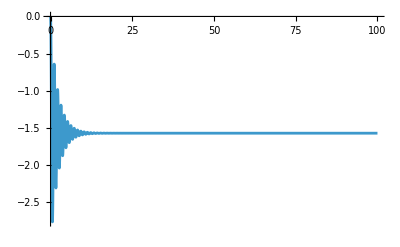

```mathematica
eqmotionnc = eqmotion/.C->0 /. data;
dsstaticnc=NDSolve[{eqmotionnc,θ[0] == 0,θ'[0] == 0},θ[t],{t,0,100}]⟦1⟧;
Plot[θ[t]/. dsstaticnc,{t,0,100},PlotRange->All]
```

Correctly, the arm is falling  down and aligning with the direction of the gravitational force.  Now we define a function for the torque and we give it as an input to the system

```mathematica
motor={C->10*Sin[(2 π*0.1) t]} (*Function for the motor *)
e1=eqmotion/. motor/. data(*equation of motion with substituted data*)
```

{C→10 Sin[0.628319 t]}

45.6165 Cos[θ[t]]-10 Sin[0.628319 t]+1. θ'[t]+1.17 θ''[t]==0

```mathematica
ds1=NDSolve[{e1,θ[0] == 0,θ'[0] == 0},θ[t],{t,0,100}] (*Numerically solving the equation of motion from t=0 s to t=100 s*)
```

{{θ[t]→InterpolatingFunction[…][t]}}

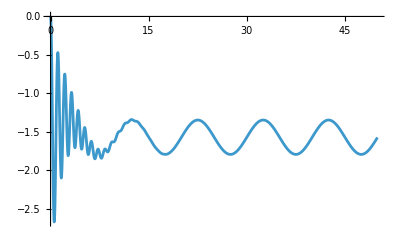

```mathematica
Plot[θ[t]/. ds1,{t,0,50},PlotRange->All] (*Plotting the whole solution*)
```

Notice that the arm starts near the vertical downward position (–π/2) because it is pulled down by gravity. The transient towards the π/2 position (direction of gravitational force) is led by the viscous and the inertial term resulting in the classical oscillations and, after that, it follows the sinusoidal input. The arm is basically falling down and the moving periodically with the desired frequency. 
The first step towards the goal of making the manipulator to track this input, is to avoid this phenomenon. To do that we have to compensate gravity such that the arm is not falling down.

## 5. Gravity (Static) Compensation

I imagine the robot being steady and still and such that the gravitational force is perpendicular to the frame (y0 in this case).This is the easiest way to identify a value of C such that the system is compensating the gravity force contribution.

```mathematica
staticeq=eqmotion/. {θ[t]->0,θ'[t]->0,θ''[t]->0} (*Substituting in the equation of motion θ[t]=0,and also its time derivatives are set to zero*)
```

-C+(g L m1)/2+g L m2==0

```mathematica
Cstatic=Solve[staticeq,C]⟦1⟧/. data (*Solving for C*)
```

{C→45.6165}

Now we use this value of C into the original equation of motion, which is a differential equation in θ[t]. And we solve numerically setting zero initial conditions.

```mathematica
eqstatic=eqmotion/. Cstatic/. data
```

-45.6165+45.6165 Cos[θ[t]]+1. θ'[t]+1.17 θ''[t]==0

Let’s check now if, with this value of C, the robot stays in the 0 position in time.

```mathematica
dsstatic=NDSolve[{eqstatic,θ[0] == 0,θ'[0] == 0},θ[t],{t,0,100}]⟦1⟧
```

{θ[t]→InterpolatingFunction[…][t]}

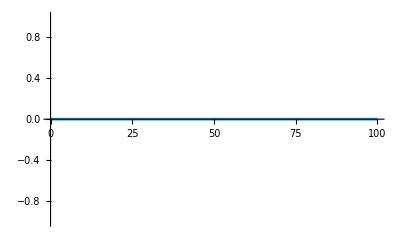

```mathematica
Plot[θ[t]/. dsstatic,{t,0,100},PlotRange->All]
```

As expected, the robot, without external excitation, is not moving from it’s 0 position.

## 6. Compliant transmission chain

In real applications, the motor needs a transmission to rotate the joint and this has typically some kind of compliancy. So, we consider here the presence of a compliant but conservative transmission belt between the motor and the link.

-Graphics-

-Graphics-

The angular stiffness is Ktheta, therefore C=Ktheta(θm-θ). The potential energy stored in the transmission may be calculated by integrating the torque in the sensitive variable, i.e. the distortion (θm-θ).

```mathematica
Uel=1/2Ktheta*(θm[t]-θ[t])^2 (*Elastic potential energy stored in the compliant belt*)
```

1/2 Ktheta (-θ[t]+θm[t])^2

```mathematica
LagrEl=T1+T2-Ug1-Ug2-Uel
```

-1/2 g L m1 Sin[θ[t]]-g L m2 Sin[θ[t]]-1/2 Ktheta (-θ[t]+θm[t])^2+1/6 L^2 m1 θ'[t]^2+1/2 L^2 m2 θ'[t]^2

Now, we must consider the presence of a new joint variable, θm[t], which is the motor angle. This will result in 2 equations of motion for the 2 independent variables. 
Let’s re-compute the equation of motion considering the addition of this new variable.

```mathematica
dLdθEL=D[LagrEl,θ[t]];
dLdθdotEL=D[LagrEl,θ'[t]];
part1EL=D[dLdθdot,t];
```

```mathematica
dLdθmEL=D[LagrEl,θm[t]];
dLdθmdotEL=D[LagrEl,θm'[t]];
part1mEL=D[dLdθmdotEL,t];
```

In terms of non-lagrangian components, we are basically moving the external torque from the joint level to the motor level. Now, the torque at the joint becomes an internal force and, for this reason, it can be neglected.

```mathematica
Q1el=PSP[Phi10,W01/θ'[t]]/. C->0 (*If you prefer, instead of W01/θ'[t], you can use elicoidal trasformation*)
```

-(2 F L)/3

Considering the θm coordinate, it results directly affected by the C torque.

```mathematica
Q2 = C;(*External forces acting on the motor*)
```

```mathematica
eqθ=part1EL-dLdθEL-Q1el
```

(2 F L)/3+1/2 g L m1 Cos[θ[t]]+g L m2 Cos[θ[t]]-Ktheta (-θ[t]+θm[t])+1/3 L^2 m1 θ''[t]+L^2 m2 θ''[t]

```mathematica
eqθm=part1mEL-dLdθmEL-Q2
```

-C+Ktheta (-θ[t]+θm[t])

```mathematica
eqmotθ=eqθ/. {F->α*D[θ[t],t]}
```

1/2 g L m1 Cos[θ[t]]+g L m2 Cos[θ[t]]-Ktheta (-θ[t]+θm[t])+2/3 L α θ'[t]+1/3 L^2 m1 θ''[t]+L^2 m2 θ''[t]

```mathematica
eqmotθm=eqθm
```

-C+Ktheta (-θ[t]+θm[t])

```mathematica
motor
```

{C→10 Sin[0.628319 t]}

```mathematica
e1el=Simplify[eqmotθ/. data/. motor/. Ktheta->10] == 0 
e2el=(eqmotθm/. data/. motor/. Ktheta->10) == 0
```

45.6165 Cos[θ[t]]+10 θ[t]-10 θm[t]+1. θ'[t]+1.17 θ''[t]==0

-10 Sin[0.628319 t]+10 (-θ[t]+θm[t])==0

```mathematica
dsel=NDSolve[{e1el,e2el,θ[0] == 0,θ'[0] == 0,θm[0] == 0},{θ[t],θm[t]},{t,0,50}]
```

{{θ[t]→InterpolatingFunction[…][t],θm[t]→InterpolatingFunction[…][t]}}

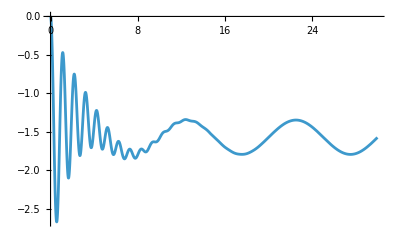

```mathematica
Plot[θ[t]/. dsel,{t,0,30},PlotRange->All]
```

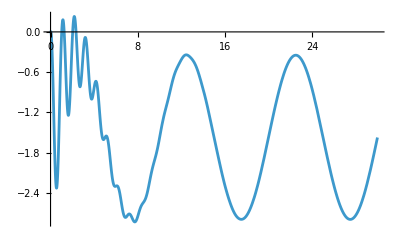

```mathematica
Plot[θm[t]/. dsel,{t,0,30},PlotRange->All]
```

These are the equations of motion.
Including a transmission gets us closer to a real scenario. Another aspect that is typical in real case applications is torque noise.

## 7. Torque noise

Applying the constant torque the arm is balanced and remains still indefinitely . However, small perturbations are present on the link produced by the external world, which are here modelled as a sinusoidal torque with a small amplitude (0.001 N*m) superimposed to the gravitational compensation torque (45.61 N*m) . We see how the system behaves under the combined action of the static torque and the perturbation.

```mathematica
newC=(C/. Cstatic)+0.001Sin[2π *0.1t] 
elbalanced=Expand[eqmotion/. C->newC/. data]
```

45.6165+0.001 Sin[0.628319 t]

-45.6165+45.6165 Cos[θ[t]]-0.001 Sin[0.628319 t]+1. θ'[t]+1.17 θ''[t]==0

```mathematica
dsbalanced=NDSolve[{elbalanced,θ[0] == 0,θ'[0] == 0},θ[t],{t,0,100}]⟦1⟧
```

{θ[t]→InterpolatingFunction[…][t]}

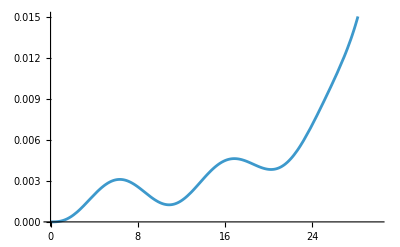

```mathematica
Plot[θ[t]/. dsbalanced,{t,0,30}]
```

The solution is unstable : this is due to the fact that the lever arm of the gravity force decreases as a cosine function and out of the horizontal configuration is no more in equilibrium . The resulting action on the link (motor constant torque + gravity torque) always pushes it upwards : this makes the equilibrium configuration (horizontal) unstable . The stabilization can be provided by a control feedback loop.

## 8. Position Control

-Graphics-

```mathematica
eqmotion
```

-C+1/2 g L m1 Cos[θ[t]]+g L m2 Cos[θ[t]]+2/3 L α θ'[t]+1/3 L^2 m1 θ''[t]+L^2 m2 θ''[t]==0

Example : we want to keep the robot arm horizontal (θd=0) in the presence of the gravity force

```mathematica
Ccontrolled=kp(θd-θ[t])/. θd->0/. kp->100; (*Proportional controller*)
```

```mathematica
elcontrolled=eqmotion/. data/. C->(Ccontrolled+0.001Sin[2π t*0.1])
```

45.6165 Cos[θ[t]]-0.001 Sin[0.628319 t]+100 θ[t]+1. θ'[t]+1.17 θ''[t]==0

Let us find the resulting behaviour in closed loop with zero initial conditions.

```mathematica
dscontrolled=NDSolve[{elcontrolled,θ[0] == 0,θ'[0] == 0},θ[t],{t,0,100}]⟦1⟧
```

{θ[t]→InterpolatingFunction[…][t]}

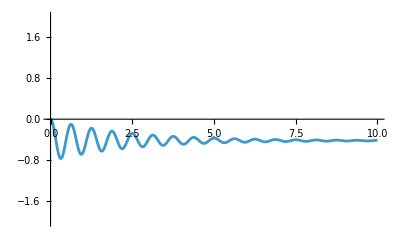

```mathematica
Plot[θ[t]/. dscontrolled,{t,0,10},PlotRange->{-2,2}]
```

The system develops an oscillation (about the steady - state rotation) at a frequency which is determined by the gain kp of the proportional feedback . A steady - state error must be present to produce a torque which balances the gravity torque. We can add the gravity compensation term that we computed earlier to move the error to 0.

```mathematica
Last@Cstatic[[1]]
```

45.6165

```mathematica
elcontrolledgc=eqmotion/. data/. C->(Ccontrolled+0.001Sin[2π t*0.1]+Last@Cstatic[[1]])
```

-45.6165+45.6165 Cos[θ[t]]-0.001 Sin[0.628319 t]+100 θ[t]+1. θ'[t]+1.17 θ''[t]==0

```mathematica
dscontrolledgc=NDSolve[{elcontrolled,θ[0] == 0,θ'[0] == 0},θ[t],{t,0,100}]⟦1⟧
```

{θ[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[θ[t]/. dscontrolledgc,{t,0,10},PlotRange->{-2,2}]
```

-Graphics-